```mathematica
Clear["`*"]

(*FibString[n] returns a list all Fibonacci strings of length n, sorted by charge sectors. A Fibonacci string is a list of 1's and 2's with no recurring 1's.*)
FibStringRecurse[1]:={{1},{2}};
FibStringRecurse[n_]:=Flatten[Map[If[Last[#]==2,{Flatten[{#,1}],Flatten[{#,2}]},{Flatten[{#,2}]}]&,FibString[n-1]],1];
FibString[n_]:=SortBy[FibStringRecurse[n],{First[#],Last[#]}&];

(*σ[n,j] returns the representation of the j:th braid group generator in the fusion space of n Fibonacci anyons, including all possible left and right charge sectors.*)
σ[n_,j_]:=Module[{fusionStates},
fusionStates=FibString[n+1];
Map[
Module[{labels,row,idx,idx2,fusionStateCopy},
fusionStateCopy=#;
labels=Take[#,{j,j+2}];
row=ConstantArray[0,Length[fusionStates]];
idx=Position[fusionStates,#][[1]][[1]];
Switch[labels,
{1,2,1},row[[idx]]=R1,
{1,2,2},row[[idx]]=Rτ,
{2,2,1},row[[idx]]=Rτ,
{2,1,2},(
row[[idx]]=B11;
fusionStateCopy[[j+1]]=2;
idx2=Position[fusionStates,fusionStateCopy][[1]][[1]];
row[[idx2]]=B12
),
{2,2,2},(
row[[idx]]=B22;
fusionStateCopy[[j+1]]=1;
idx2=Position[fusionStates,fusionStateCopy][[1]][[1]];
row[[idx2]]=B21;
)
];
row
]&
,fusionStates]
];

(*U[p] returns Subscript[σ, 1] Subscript[σ, 2]... Subscript[σ, p] Subscript[σ, p+1] Subscript[σ, p]... Subscript[σ, 2] Subscript[σ, 1] on p+2 Fibonacci anyons.*)
U[p_]:=Dot@@Flatten[{Table[σ[p+2,j],{j,1,p+1}],Table[σ[p+2,j],{j,p,1,-1}]},1];

(*Demo*)
σ[3,1]//MatrixForm
σ[3,1].σ[3,2].σ[3,1]==U[1]
```

(Rτ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | R1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Rτ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | B11 | B12 | 0 | 0 | 0
0 | 0 | 0 | B21 | B22 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | B11 | 0 | B12
0 | 0 | 0 | 0 | 0 | 0 | Rτ | 0
0 | 0 | 0 | 0 | 0 | B21 | 0 | B22)

True

eigenvalues with mult.:
ⅇ^(-(3 ⅈ π)/5) × 3, ⅇ^((4 ⅈ π)/5) × 5, ⅇ^(-(ⅈ π)/5) × 3, ⅇ^((ⅈ π)/5) × 2,

det(U_p) = 1

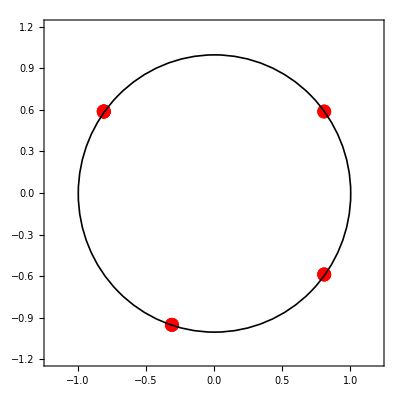

```mathematica
(*PlotComplex[{a,b,c}] plots the complex numbers a,b,c on the complex unit circle.*)
PlotComplex[data_]:=Module[{p},
p=ListPlot[{Re[#],Im[#]}&/@data,AxesOrigin->{0,0},PlotRange->{{-1.2,1.2},{-1.2,1.2}},AspectRatio->1,Frame->True,PlotStyle->Directive[Red,PointSize[.025]]];Show[p,Graphics[{Thickness[0.003],Circle[{0,0},1]}]]
];

(*This is to force conversion to polar form, implicitly assuming we are on the complex unit circle.*)
ComplexToPolar[z_]:=E^(I Rationalize[Arg[z]/Pi]Pi);

(*Plug in values for the parameters.*)
R1=Exp[4Pi I/5];
Rτ=Exp[-3Pi I/5];
R=({{R1, 0}, {0, Rτ}});
φ=GoldenRatio;
F=({{φ^-1, φ^(-1/2)}, {φ^(-1/2), -φ^-1}});
B=Inverse[F].R.F;
B11=B[[1,1]];
B12=B[[1,2]];
B21=B[[2,1]];
B22=B[[2,2]];
(*Count and plot eigenvalues. Play around with p in U[p].*)
ev=U[2]//N//Eigenvalues//ComplexToPolar;(*Computing without N[..] is super slow for large p.*)
Print["eigenvalues with mult.:\n",StringJoin[Map[ToString[#,TraditionalForm]<>" × "<>ToString[Count[ev,#]]<>", "&,DeleteDuplicates[ev]]]];
Print["det(U_p) = ",Times@@ev];
PlotComplex[ev]
```

```mathematica
Table[Rationalize[Arg[Det[N[σ[n,1]]]]/Pi]Pi,{n,2,16}]
```

{-π/5,-(3 π)/5,-(4 π)/5,(3 π)/5,-π/5,(2 π)/5,π/5,(3 π)/5,(4 π)/5,-(3 π)/5,π/5,-(2 π)/5,-π/5,-(3 π)/5,-(4 π)/5}

```mathematica
MapIndexed[Function[{arg,idx},Mod[arg*(2(idx[[1]]-1)+1),2Pi]],{-π/5,-3π/5,-4π/5,3π/5,-π/5,2π/5,π/5,3π/5,4π/5,-3π/5,π/5,-2π/5,-π/5,-3π/5,-4π/5}]
```

{(9 π)/5,π/5,0,π/5,π/5,(2 π)/5,(3 π)/5,π,(8 π)/5,(3 π)/5,π/5,(4 π)/5,π,(9 π)/5,(4 π)/5}

```mathematica
Table[Rationalize[Arg[Eigenvalues[σ[n,j]]]/Pi]Pi,{n,2,5},{j,1,n-1}]
```

{{{(4 π)/5,(4 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5}},{{(4 π)/5,(4 π)/5,(4 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5},{(4 π)/5,(4 π)/5,(4 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5}},{{(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5},{(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5},{(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5}},{{(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5},{(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5},{(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5},{(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,(4 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5,-(3 π)/5}}}